```mathematica
RandomVariate[MultinormalDistribution[{0,0},IdentityMatrix[2]],5]//Grid
```

0.0701407 | 1.46745
-0.0934907 | -0.0298328
0.0984031 | -0.277896
-0.58026 | -2.43467
-1.67605 | 0.822558

```mathematica
sample[center_,num_Integer]:=RandomVariate[
MultinormalDistribution[center,{{1,0},{0,1}}],
num];
```

```mathematica
clusters={sample[{-3,-3},10000],sample[{3,3},10000]};
```

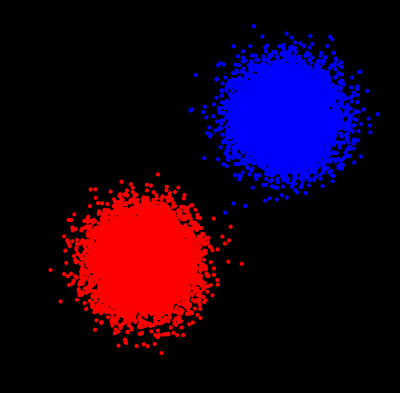

```mathematica
scatterplot=Graphics[
MapThread[{#1,Point[#2]}&,{{Red,Blue},clusters}],
Background->Black,
PlotRange->10,
Axes->True]
```

```mathematica
net=NetChain[{
DotPlusLayer[400],
ElementwiseLayer[Ramp],
DotPlusLayer[2],
SoftmaxLayer[]
},
"Input"->{2},
"Output"->NetDecoder[{"Class",{Red,Blue}}]
]
```

NetChain[]

```mathematica
net=NetInitialize[net]
```

NetChain[]

```mathematica
NetGraph[net]
```

NetGraph[]

```mathematica
SoftmaxLayer[][{1,2,3}]
```

```mathematica
Total[{0.09003057330846786,0.2447284758090973,0.6652409434318542}]
```

1.

```mathematica
softmax[z_]:=Module[{e=Exp[z]},e/Total[e]]
```

```mathematica
softmax[{1,2,3}]
```

{ⅇ/(ⅇ+ⅇ^2+ⅇ^3),ⅇ^2/(ⅇ+ⅇ^2+ⅇ^3),ⅇ^3/(ⅇ+ⅇ^2+ⅇ^3)}

```mathematica
SoftmaxLayer[][{1,2}]
```

{0.268941,0.731059}

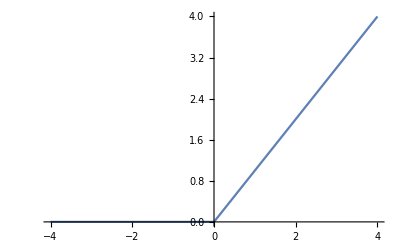

```mathematica
Plot[Ramp[x],{x,-4,4}]
```

```mathematica
net[{0,0}]
```

RGBColor[0, 0, 1]

```mathematica
data=RandomSample[
Join@@MapThread[
Thread[#1->#2]&,
{clusters,{Red,Blue}}
]];
```

```mathematica
Length[data]
```

20000

```mathematica
RandomSample[data,5]//Column
```

{-0.875766,-2.25447}→RGBColor[1, 0, 0]
{-1.21358,-1.30929}→RGBColor[1, 0, 0]
{3.72463,1.27932}→RGBColor[0, 0, 1]
{0.791102,-0.77576}→RGBColor[1, 0, 0]
{1.17921,1.58983}→RGBColor[0, 0, 1]

```mathematica
training=data[[;;18000]];
validation=data[[18001;;]];
```

```mathematica
RandomSample[training,5]//Column
```

{2.83749,1.26845}→RGBColor[0, 0, 1]
{1.09485,2.65967}→RGBColor[0, 0, 1]
{-2.13354,-4.10983}→RGBColor[1, 0, 0]
{1.84687,1.83535}→RGBColor[0, 0, 1]
{3.67629,1.19999}→RGBColor[0, 0, 1]

```mathematica
net[{1,1}]
```

RGBColor[0, 0, 1]

```mathematica
net[{-1,-1}]
```

RGBColor[1, 0, 0]

```mathematica
result=NetTrain[net,training,
ValidationSet->validation,
TargetDevice->"GPU",
MaxTrainingRounds->10000]
```

NetChain[]

```mathematica
result[{0,0}]
```

RGBColor[1, 0, 0]

```mathematica
validation[[2]]
```

{-1.70149,-0.512526}→RGBColor[1, 0, 0]

```mathematica
cm=ClassifierMeasurements[result,validation]
```

ClassifierMeasurementsObject[…]

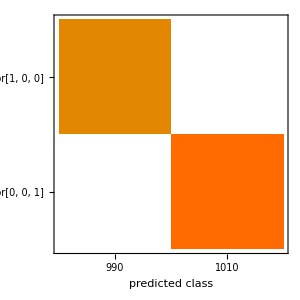

```mathematica
cm["ConfusionMatrixPlot"]
```

```mathematica
cm["Accuracy"]
```

1.

```mathematica
First[Values[result[{0,0},"Probabilities"]]]
```

0.565093

```mathematica
f[x_,y_]:=First[Values[result[{x,y},"Probabilities"]]]
```

Values::invrl: The argument … is not a valid Association or a list of rules.

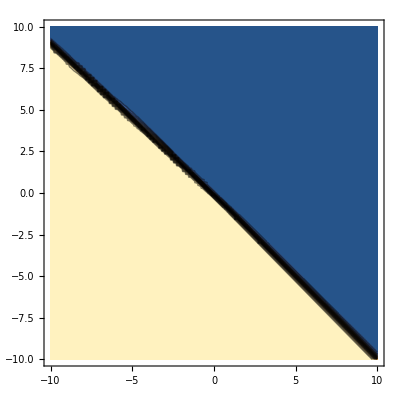

```mathematica
contourplot=ContourPlot[
f[x,y],
{x,-10,10},{y,-10,10},
Contours->20]
```

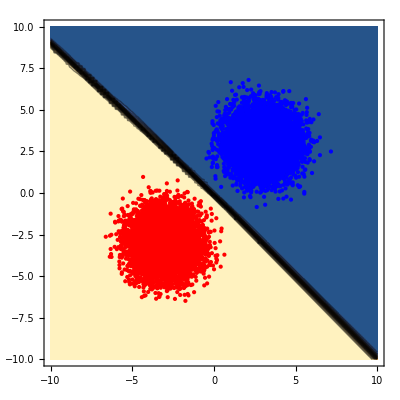

```mathematica
Show[{contourplot,scatterplot}]
```